```mathematica
MINISTERUL EDUCAȚIEI ȘI CERCETĂRII AL REPUBLICII MOLDOVA

Universitatea Tehnică a Moldovei

Facultatea Calculatoare,Informatică şi Microelectronică

Departamentul Informatică şi Ingineria Sistemelor









RAPORT

Lucrare de laborator nr.3

la cursul „Probabilitate și statistică aplicată”









A efectuat:                St.gr.CR-221FR Serba Cristina

A verificat:                    Andrievschi-Bagrin Veronica













Chișinău 2023
```

Sarcina 1
Este dată repartiţia v.a. de tip discret ξ: x1=-2, x2=-1, x3=0, x4=1, p1=0,2, p2=0,4, p3=0,3, p4=0,1; Se cere: 
1) să se introducă în Sistemul Mathematica repartiţia v.a.d. ξ

```mathematica
p={{-2,-1,0,1},{0.2,0.4,0.3,0.1}}
```

{{-2,-1,0,1},{0.2,0.4,0.3,0.1}}

```mathematica
MatrixForm[p]
```

(-2 | -1 | 0 | 1
0.2 | 0.4 | 0.3 | 0.1)

2) funcţia de repartiţie şi graficul ei;

```mathematica
F[x_]:=0/;x<=-2;F[x_]:=0.2/;-2<x<=-1;F[x_]:=0.6/;-1<x<=0;F[x_]:=0.9/;0<x<=1;
F[x_]:= 1/;1<x;
```

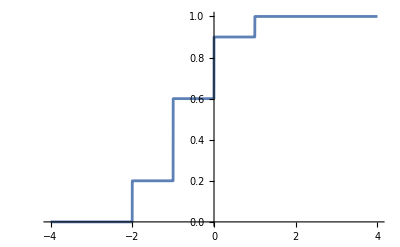

```mathematica
Plot[F[x],{x,-4,4}]
```

3) probabilitatea ca ξ  va lua valori din intervalul [1; 4);

```mathematica
P(1<=ξ<4)=F[4]-F[1]
```

0.1

4) valoarea medie;

```mathematica
mξ = Sum[p[[1,j]]p[[2,j]],{j,1,4}]
```

-0.7

5) dispersia;

```mathematica
Dξ =Sum[((p[[1,j]]-mξ )^2)p[[2,j]],{j,1,4}]
```

0.81

6) abaterea medie pătratică;

```mathematica
σξ =Sqrt[Dξ ]
```

0.9

7) momentele iniţiale de ordine până la 4 inclusiv;

```mathematica
α1=Sum[((p[[1,j]]^1)p[[2,j]]),{j,1,4}]
```

-0.7

```mathematica
α2=Sum[((p[[1,j]]^2)p[[2,j]]),{j,1,4}]
```

1.3

```mathematica
α3=Sum[((p[[1,j]]^3)p[[2,j]]),{j,1,4}]
```

-1.9

```mathematica
α4=Sum[((p[[1,j]]^4)p[[2,j]]),{j,1,4}]
```

3.7

8) momentele centrate de ordine până la 4 inclusiv;

```mathematica
μ1 = Sum[((p[[1,j]]-mξ)^1)p[[2,j]],{j,1,4}]
```

1.11022×10^-16

```mathematica
μ2 = Sum[((p[[1,j]]-mξ)^2)p[[2,j]],{j,1,4}]
```

0.81

```mathematica
μ3 = Sum[((p[[1,j]]-mξ)^3)p[[2,j]],{j,1,4}]
```

0.144

```mathematica
μ4 = Sum[((p[[1,j]]-mξ)^4)p[[2,j]],{j,1,4}]
```

1.4817

9) asimetria;

```mathematica
Sk[ξ]=μ3/(σξ ^3)
```

0.197531

10) excesul

```mathematica
Ex[ξ]=μ4/((σξ ^4)-3)
```

-0.632152

```mathematica
Clear[F,p,mξ,Dξ ,σξ,α1,α3,α2,α4,μ1,μ2,μ3,μ4,Sk,Ex]
```

Sarcina 2
Presupunem că probabilitatea statistică că un copil nou
născut să fie băiat este egală cu 0.51. Se cere:
1) să se determine repartiţia v.a. ξ care reprezintă numărul de băieţi printre 1000 de copii noi născuţi;

p(k) = P(ξ =k)=P1000(k)=binomial(1000, k) (0.51^k×0.49^(1000 - k))
, k = 0, 1, 2,…, 1000

2) să se calculeze probabilitatea că printre 1000 de copii noi născuţi numărul băieţilor va fi cuprins între 300+k şi 500+k, unde k este numărul variantei.

```mathematica
N[Sum[(1000!*((0.51)^k)*((0.49)^(1000-k)))/((k!)*((1000-k))!),{k,366,566}]]
```

0.999828

Sarcina 3
Numărul ξ de particule alfa emise de un gram de substanţă radioactivă într-o secundă este o v.a.d. cu repartiţia Poisson cu parametrul a, unde a este numărul mediu de particule alfa emise într-o secundă. 1) Să se determine seria de repartiţie a v.a.d. ξ. 

pk = P(ξ=k) = ((a^k)/(k!))*e^(-a), k = 0, 1, 2, ...

2) Să se calculeze probabilităţile evenimentelor: A = { într-o
secundă vor fi emise nu mai mult de două particule alfa} şi B = { într-o secundă vor fi emise cinci particule alfa}, C = { într-o secundă vor fi emise mai mult de zece particule alfa}. Care este numărul de particule alfa care corespunde celei mai mari probabilităţi? Să se considere că a=1+0,25n, unde n este numărul variantei.
1. P(A) = P(ξ =0)+P(ξ=1)+P(ξ=2)

```mathematica
N[(17.5^0/0!*e^(-17.5))+(17.5^1/1!*e^(-17.5))+(17.5^2/2!*e^(-17.5))]
```

171.625/e^17.5

2. P(B) = P(ξ=5)

```mathematica
N[17.5^5/5!*e^(-17.5)]
```

13677.6/e^17.5

3.P(C) =1-P(ξ=10)

```mathematica
N[1-(17.5^10/10!*e^(-17.5))]
```

1.-742365./e^17.5

Pentru k > 10 probabilitatea este cea mai mare 1.-742365./e^17.5 = 0.98135...

Sarcina 4
1. Să se scrie legea de repartiţie a variabilei aleatoare ξ  care reprezintă numărul de aruncări nereuşite ale unui zar până la prima apariţie a numărului 4. 

Notăm cu A evenimentul care constă în apariția numărului 4 și cu N evenimentul care constă în apariția oricărui alt număr. 
N = !A
Cum un zar are 6 fețe, rezultă că P(A) = 1/6 și P(N) = 1-1/6 = 5/6
Pentru ca numărul 4 sa apară prima dată avem probabilitatea p1=P(A) . Pentru ca să apară a doua oară avem p2=P(ξ=2)=P(!A and A). Pentru ca să apară la aruncarea k, ξ va lua valoarea k. Astfel, legea de repartiție a variabilei aleatoare ξ este:
pk=A(ξ=k)=(!A and  ... and !A and A) = 1/6*(5/6)^(k-1), k = 1, 2, ...

2. Să se calculeze probabilitatea că numarul aruncărilor nereuşite va varia între 5+k si 15+k , unde k este numărul variantei.

```mathematica
N[Sum[1/6*((5/6)^(k-1)),{k,71,81}]]
```

2.48048×10^-6

Sarcina 5
V.a.c. ξ este definită de densitatea sa de repartiţie f(x).
-Graphics-
Să se determine: 1) reprezentarea v.a.c. ξ în Sistemul Mathematica;

```mathematica
f[x_]:=0/;x<1;f[x_]:=2*x-2/;1<=x<=2;f[x_]:=0/;x>2
```

2) linia de repartiţie;

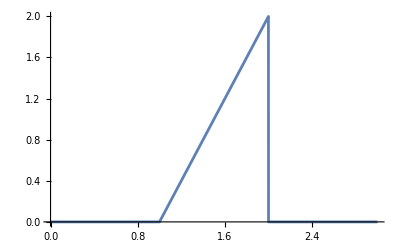

```mathematica
Plot[f[x],{x,0,3}]
```

3) funcţia de repartiţie F(x) şi graficul ei

Cum toate valorile posibile ale V.a.c. ξ aparțin segmentului [1,2] , rezulta că F(x) = 0, x<1 si F(x) = 1,x>2

```mathematica
F1[x] = Integrate[2*t-2,{t,1,x}]
```

-2 (-1+x)+2 (-1/2+x^2/2)

```mathematica
F[x_]:=0/;x<0;F[x_]:=-2 (-1+x)+2 (-1/2+x^2/2)/;1<=x<=2;F[x_]:=1/;x>2
```

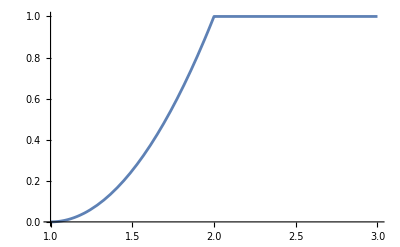

```mathematica
Plot[F[x],{x,1,3}]
```

4) valoarea ei medie;

```mathematica
mξ = NIntegrate[x*f[x],{x,1,2}]
```

1.66667

5) dispersia

```mathematica
Dξ = N[Integrate[(x-mξ)^2*f[x],{x,1,2}]]
```

0.0555556

6) abaterea medie pătratică

```mathematica
σξ = Sqrt[Dξ]
```

0.235702

7) coeficientul de variaţie;

```mathematica
vξ = σξ/mξ
```

0.141421

8) momentele iniţiale de ordinele până la 4 inclusiv,
Momentul iniţial α1 coincide cu speranţa matematică şi deci α1 = mξ = 1.66667

```mathematica
α2 =NIntegrate[x^2*f[x],{x,1,2}]
```

2.83333

```mathematica
α3 =NIntegrate[x^3*f[x],{x,1,2}]
```

4.9

```mathematica
α4 =NIntegrate[x^4*f[x],{x,1,2}]
```

8.6

9) momentele centrale de ordinele până la 4 inclusiv
Momentul centrat de ordinul 1 este egal cu zero pentru orice v.a.: μ1 = 0. Momentul centrat de ordinul doi coincide cu dispersia şi deci μ2 = Dξ  = 2

```mathematica
μ3=N[Integrate[(x-mξ )^3*f[x],{x,1,2}]]
```

-0.00740741

```mathematica
μ4=N[Integrate[(x-mξ )^4*f[x],{x,1,2}]]
```

0.00740741

10) asimetria

```mathematica
Sk[ξ] =μ3/(σξ)^3
```

-0.565685

11) excesul;

```mathematica
Ex[ξ]=μ4/(σξ)^4-3
```

-0.6

12) probabilitatea ca ξ va lua valori din prima jumătate a intervalului de valori posibile.

```mathematica
NIntegrate[f[x],{x,1,1.5}]
```

0.25

```mathematica
Clear[f,F,mξ,Dξ ,σξ,α1,α3,α2,α4,μ1,μ2,μ3,μ4,Sk,Ex]
```

Sarcina 6
V.a. ξ are repartiţia normală cu valoarea medie m şi cu abaterea medie pătratică σ. (m=5, σ=2, α=2, β=6) 1) să se instaleze pachetul de programe Statistics`NormalDistribution`
2) să se definească (introducă) v.a.c. dată

```mathematica
rn=NormalDistribution[5,2]
```

NormalDistribution[5,2]

3) să se definească (determine) densitatea de repartiţie ;

```mathematica
drn = PDF[rn,x]
```

(ⅇ^(-1/8 (-5+x)^2))/(2 √(2 π))

4) să se construiască linia de repartiţie

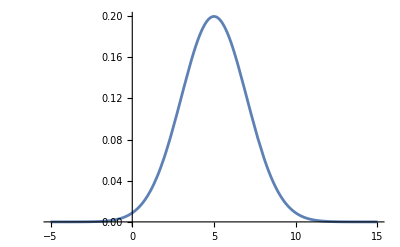

```mathematica
Plot[drn,{x,-5,15}]
```

5) să se definească (determine) funcţia de repartiţie ;

```mathematica
frn=CDF[rn,x]
```

1/2 Erfc[(5-x)/(2 √2)]

6) să se construiască graficul funcţiei de repartiţie

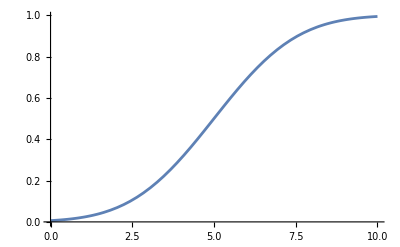

```mathematica
Plot[frn,{x,0,10}]
```

7) să se construiască pe acelaşi desen graficele densităţii de repartiţie şi al funcţiei de repartiţie

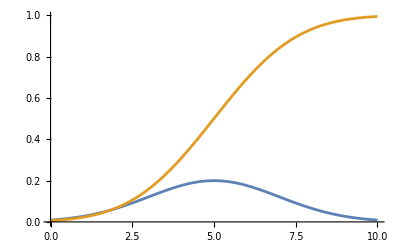

```mathematica
Plot[{drn,frn},{x,0,10}]
```

8) să se construiască pe acelaşi desen gfaficele densităţii de repartiţie şi al funcţiei de repartiţie astfel, ca grosimea graficului densităţii de repartiţie să fie egală cu 0,5 din grosimea standard, iar grosimea graficului funcţiei de repartiţie să fie egală cu 0,9 din grosimea standard;

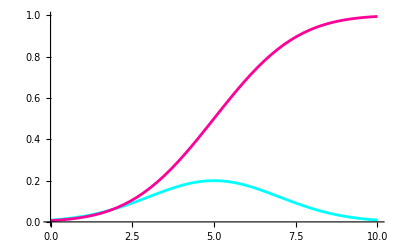

```mathematica
Plot[{drn,frn},{x,0,10},PlotStyle->{Hue[0.5],Hue[0.9]}]
```

9) Să se calculeze probabilitatea ca ξ să ia valori din intervalul [α, β].

```mathematica
NIntegrate[drn,{x,2,6}]
```

0.624655

```mathematica
Clear[rn,drn,frn]
```

Sarcina 7
Înălţimea unui bărbat este o v.a. cu repartiţia normală. Presupunem că această repartiţie are parametrii m=175+(-1)^n/n cm şi σ=6-(-1)^n/n cm. Să se formeze programul de conficţionate a costumelor bărbăteşti pentru o fabrică de confecţii care se referă la asigurarea cu costume a bărbaţilor, înălţimile cărora aparţin intervalelor: [150, 155), [155, 160), [160, 165), [165, 170), [170, 175), [175, 180), [180, 185), [185, 190), [190, 195), [195, 200], n fiind numarul variantei

```mathematica
rn =NormalDistribution[175.015151515,5.984848485]
```

NormalDistribution[175.015,5.98485]

```mathematica
drn = PDF[rn,x]
```

0.0666587 ⅇ^(-0.0139593 (-175.015+x)^2)

```mathematica
N[Integrate[drn,{x,150,155}]]
```

0.000397855

```mathematica
N[Integrate[drn,{x,155,160}]]
```

0.00564361

```mathematica
N[Integrate[drn,{x,160,165}]]
```

0.0410665

```mathematica
N[Integrate[drn,{x,165,170}]]
```

0.1539

```mathematica
N[Integrate[drn,{x,170,175}]]
```

0.297968

```mathematica
N[Integrate[drn,{x,175,180}]]
```

0.298563

```mathematica
N[Integrate[drn,{x,180,185}]]
```

0.154825

```mathematica
N[Integrate[drn,{x,185,190}]]
```

0.0414793

```mathematica
N[Integrate[drn,{x,190,195}]]
```

0.00572338

```mathematica
N[Integrate[drn,{x,195,200}]]
```

0.000405119

Sarcina 8
Presupunem că o convorbire telefonică durează în medie 5 minute şi este o v.a. ξ de repartiţie exponenţială. 1) Să se introducă în Sistemul Mathematica d.r. a v.a.c. ξ.

```mathematica
f[x_]:=5*Exp[(-5*x)]/;x>=0;f[x_]:=0/;x<0
```

2) Să se determine funcţia de repartiţie şi să se construiască graficul ei.

```mathematica
F[x_]:=1-Exp[(-5*x)]/;x>0;F[x_]:=0/;x<=0
```

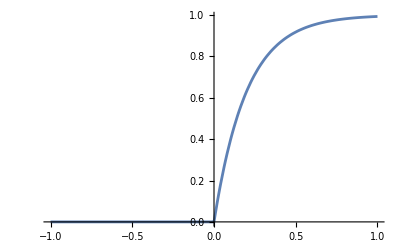

```mathematica
Plot[F[x],{x,-1,1}]
```

3) Dacă vă apropriaţi de o cabină telefonică imediat după ce o
persoană a întrat în ea atunci care este probabilitatea că o să aşteptaţi nu mai mult de 2+n/3 minute, unde n este numărul variantei?

```mathematica
Integrate[5*Exp[(-5*x)],{x,0,24}]
```

1-1/ⅇ^120

```mathematica
∫_0^24 f[x]ⅆx
```

∫_0^24 f[x]ⅆx

Sarcina 9
Un autobuz circulă regulat cu intervalul 30 minute. 1) Să se scrie în Sistemul Mathematica d.r. a v.a.c. ξ care reprezintă durata aşteptării autobuzului de către un pasager care soseste în staţie într-un moment aleator de timp.

```mathematica
f[x_]:=0/;x<0;
f[x_]:=1/30/;0<=x<=30;f[x_]:=0/;x>30
```

2) Să se construiască linia de repartiţie.

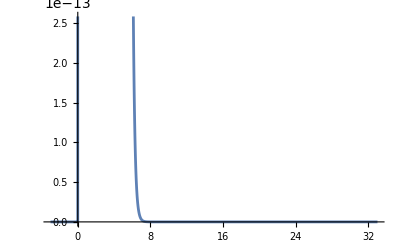

```mathematica
Plot[f[x],{x,-3,33}]
```

3) Să se determine f.r.e şi să se construiască graficul ei

```mathematica
F[x_]:=0/;x<0;F[x_]:=x/30/;0<=x<=30;F[x_]:=1/;x>30
```

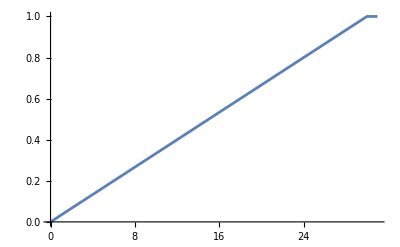

```mathematica
Plot[F[x],{x,0,31}]
```

4) Care este probabilitatea că, sosind în staţie, pasagerul va aştepta autobuzul nu mai mult de 10+n/2 minute, unde numărul n coincide cu numărul variantei?

```mathematica
P= Integrate[1/30,{x,0,2}]
```

1/15

Sarcina 10
Cantitatea anuală de precipitaţii atmosferice are repartiţie normală. Presupunem că anual, cantitatea de precipitaţii într-o anumită regiune este o v.a. aleatoare de repartiţie normală de parametrii m = 500 (mm) şi σ = 150. 
1. Care este probabilitatea că în anul viitor cantitatea de precipitaţii va fi cuprinsă între 400+5n şi 500+5n, unde n este numărul variantei.

```mathematica
rn=NormalDistribution[500,150]
```

NormalDistribution[500,150]

```mathematica
drn = PDF[rn,x]
```

(ⅇ^(-(-500+x)^2/45000))/(150 √(2 π))

```mathematica
NIntegrate[drn,{x,730,830}]
```

0.0486934

2. Dacă considerăm că un an este secetos când cantitatea de precipitaţii nu depăşeşte 300 mm, atunci care este probabilitatea că doi din viitorii zece ani vor fi secetoşi?

Vom folosi formula binomiala unde -Graphics-, deci 
probabilitatea ca un an va fi secetos este:

```mathematica
N[Integrate[(Exp[-((x-500)^2)/45000])/(150*Sqrt[2*Pi]),{x,0,300}]]
```

0.0907822

Probabilitatea ca 2 din 10 ani vor fi secetosi:

```mathematica
p = 0.0907822
q = 1 -p
P = N[(10!*p^2*q^8)/(2!*(10-2)!)]
```

0.0907822

0.909218

0.173204